```mathematica
Limit[((Sin[x]+x^3)^(1/3)-x)/x^5,x-> 0]
```

Indeterminate

```mathematica
Indeterminate

Integrate[Log[x]/((x^2+1)^2),{x,0,∞}]
```

Indeterminate

-π/4

```mathematica
H={{Δ,Ω},{Ω,Δ}};
{eigenvalues,eigenvectors}=Eigensystem[H];


normalizedEigenvectors=Map[#/Norm[#]&,eigenvectors];


Print["Vlastné hodnoty: ",eigenvalues];
Print["Normalizované vlastné vektory:"];
Scan[Print[MatrixForm[#]]&,normalizedEigenvectors];
```

Vlastné hodnoty: {Δ-Ω,Δ+Ω}

Normalizované vlastné vektory:

(-1/(√2)
1/(√2))

(1/(√2)
1/(√2))

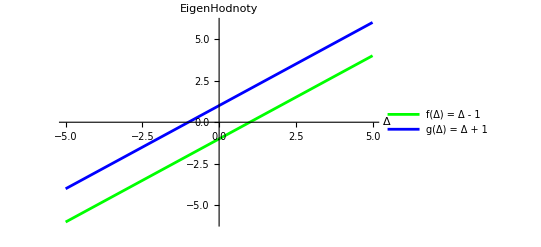

```mathematica
f[Δ_]:=Δ-1
g[Δ_]:=Δ+1

Plot[{f[Δ],g[Δ]},{Δ,-5,5},PlotStyle->{Green,Blue},AxesLabel->{"Δ","EigenHodnoty"},PlotLegends->{"f(Δ) = Δ - 1","g(Δ) = Δ + 1"}]
```

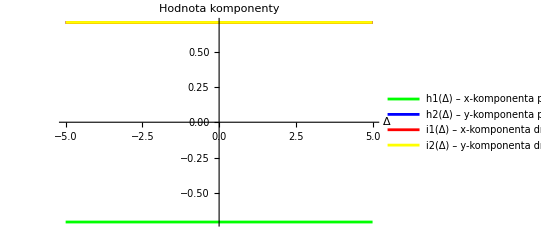

```mathematica
h1[Δ_]:=-1/Sqrt[2]
h2[Δ_]:=1/Sqrt[2]
i1[Δ_]:=1/Sqrt[2]
i2[Δ_]:=1/Sqrt[2]

Plot[{h1[Δ],h2[Δ],i1[Δ],i2[Δ]},{Δ,-5,5},PlotStyle->{Green,Blue,Red,Yellow},AxesLabel->{"Δ","Hodnota komponenty"},PlotLegends->{"h1(Δ) – x-komponenta prvého vlastného vektora","h2(Δ) – y-komponenta prvého vlastného vektora","i1(Δ) – x-komponenta druhého vlastného vektora","i2(Δ) – y-komponenta druhého vlastného vektora"}]
```

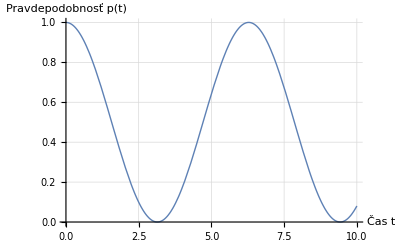

```mathematica
ψ0={{1},{0}};

ψ0dual=ConjugateTranspose[ψ0];
H[Δ_,Ω_]:={{Δ,Ω},{Ω,Δ}};
U[t_,Δ_,Ω_]:=MatrixExp[-I*H[Δ,Ω]*t];
ψ[t_,Δ_,Ω_]:=U[t,Δ,Ω].ψ0;
p[t_,Δ_,Ω_]:=Abs[ψ0dual.ψ[t,Δ,Ω]][[1,1]]^2;
Δvalue=1;
Ωvalue=0.5;


Plot[p[t,Δvalue,Ωvalue],{t,0,10},AxesLabel->{"Čas t","Pravdepodobnosť p(t)"},PlotRange->{0,1},GridLines->Automatic,PlotStyle->Thick]
```